#### 23.05.2021 (Визуализация случайных блужданий и тензора инерции (Pellisetto))

Грубая программа запуска случайных блужданий

```mathematica
SAW={{0,0}};
n=100;
i=1;
step=0;


While[(i<n)&&(step<2n)&&(i>0),
Neigh =Table[Last[SAW]+turn,{turn,{{0,1},{0,-1},{1,0},{-1,0}}}];
For[j=4,j>0,j--,
If[MemberQ[SAW,Neigh[[j]]],Neigh=Delete[Neigh, j]];];
If[Length[Neigh]>0,,AppendTo[Neigh,"del"]];
new=RandomChoice[Neigh];
SAW=If[StringQ[new],Delete[SAW,Length[SAW]],Append[SAW,new]];
i=Length[SAW];
step=step+1;
];



If[i==0,Print["Не повезло-не повезло"]];
If[i==n,Print["Повезло-повезло"]];
If[0<i<n,Print["Не совсем повезло: ", i]];
```

Повезло-повезло

Получили график случайного блуждания

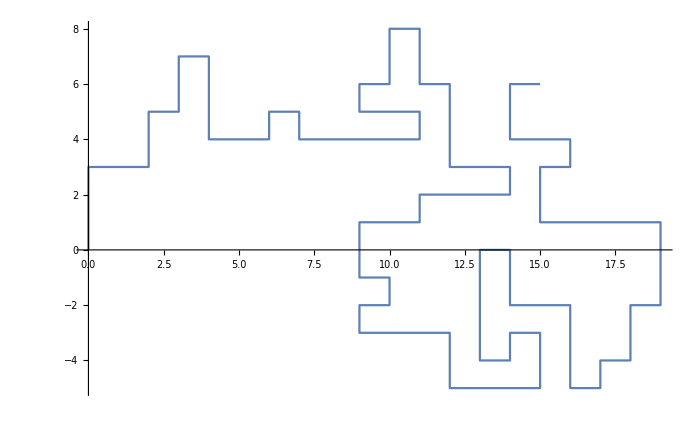

```mathematica
walk=ListPlot[SAW,Joined->True,ImageSize->700,PlotRange->All]
```

#### Попробуем рассчитать эллипсоид вращения в системе координат с центром масс в начале координат:

.

.

.

Обработка данных блуждания...

Центр координат - {3,11/2}

Центр новых координат - {0,0}

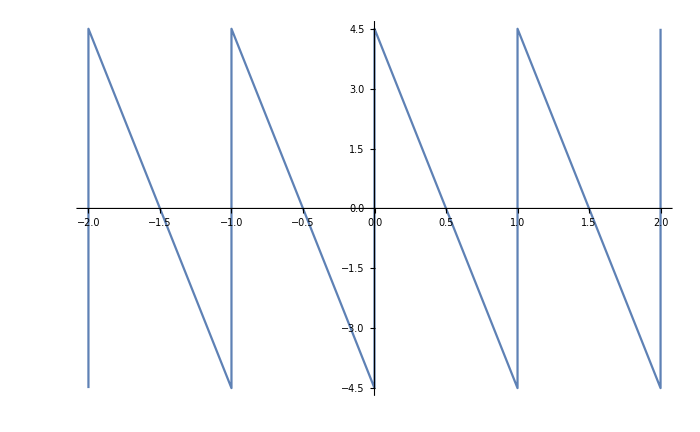

Радиус инерции - 41/4

```mathematica
Do[Print["."],3]
Print[Style["Обработка данных блуждания...", 20]];
center=Total[SAW]/n;
Print["Центр координат - ", center];
SAWc=Map[#-center&,SAW];
n=Length[SAWc];
centerC=Total[SAWc]/n;
Print["Центр новых координат - ", centerC];
Walkc=ListPlot[SAWc,Joined->True,ImageSize->700,PlotRange->All]
Rg2 = Total[Table[SAWc[[i]][[1]]^2+SAWc[[i]][[2]]^2,{i,1,n}]]/n;
Print["Радиус инерции - ", Rg2];
```

#### Теперь попробуем рассчитать тензор инерции и соответственно эллипсоид инерции для того же

{{825/2,0},{0,100}}

Тензор инерции - (825/2 | 0
0 | 100)

Найдём собственные значения (размеры полуосей) и Жорданов базис (для определения поворота эллипса)

Собственные значения - {412.5,100.}

Собственные вектора - {{1.,0.},{0.,1.}}

Жорданова матрица - (412.5 | 0.
0. | 100.)

Найдём по нормализованным собственным векторам угол поворота - именно на него мы и повернём наш эллипс

Угол поворота (в радианах) - 0.

Итоговое изображение:

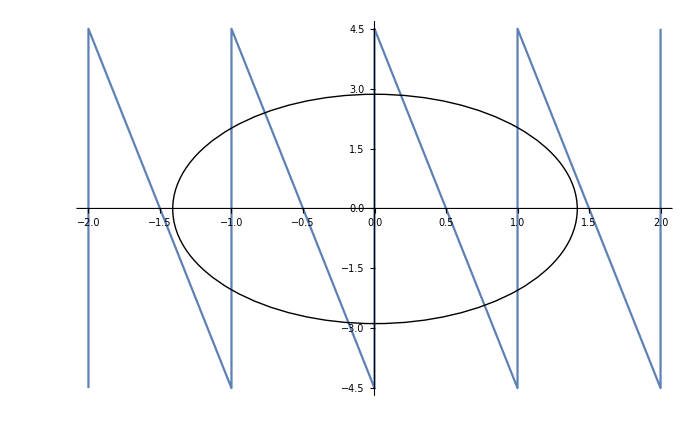

{1.41421,2.87228}

```mathematica
Jxx = Total [Table[SAWc[[i]][[2]]^2,{i,1,n}]];
Jyy = Total [Table[SAWc[[i]][[1]]^2,{i,1,n}]];
Jxy=-Total[Table[SAWc[[i]][[1]]*SAWc[[i]][[2]],{i,1,n}]];
J = {{Jxx, Jxy},{Jxy, Jyy}}
Print["Тензор инерции - ",  J//MatrixForm];
Print[Style["Найдём собственные значения (размеры полуосей) и Жорданов базис (для определения поворота эллипса)", Red]]
AB=N[Eigenvalues[J]];
Print["Собственные значения - ", AB];
S=Map[Normalize,N[Eigenvectors[J]]];
Print["Собственные вектора - ", S];
Jd=N[Inverse[Transpose[S]].J.Transpose[S]];
Print["Жорданова матрица - ", Jd//MatrixForm];
Print[Style["Найдём по нормализованным собственным векторам угол поворота - именно на него мы и повернём наш эллипс", Red]];
α= ArcCos[S[[1]][[1]]];
Print["Угол поворота (в радианах) - ", α];
ell2=Graphics[Rotate[Circle[centerC,Reverse[√(AB/n)]],α]];
Print[Style["Итоговое изображение:",20]]
Show[Walkc,ell2,PlotRange->All]
Print[Reverse[√(AB/n)]]
```

```mathematica
SAW=Join[Array[{0,#}&, 10, 0],Array[{#,10}&,10,0],Array[{10,10-#}&,10,0],Array[{10-#,0}&,10,0]]
```

{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{10,9},{10,8},{10,7},{10,6},{10,5},{10,4},{10,3},{10,2},{10,1},{10,0},{9,0},{8,0},{7,0},{6,0},{5,0},{4,0},{3,0},{2,0},{1,0}}

```mathematica
{{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10},{10,10},{10,9},{10,8},{10,7},{10,6},{10,5},{10,4},{10,3},{10,2},{10,1},{10,0},{9,0},{8,0},{7,0},{6,0},{5,0},{4,0},{3,0},{2,0},{1,0}}
```

```mathematica
SAW=Flatten[Array[{#1,#2}&,{5,10}],1];
```